{{y[x]→1/2 ⅇ^(-x^2/2) (2+√(2 π) Erfi[x/(√2)])}}

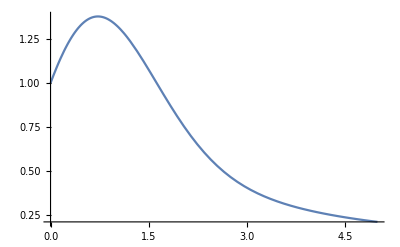

```mathematica
sol = DSolve[{y'[x]+x y[x] ==1, y[0]==1}, y[x], x]
Plot[Evaluate[y[x]/.sol],{x,0,5}, PlotRange->All]
```